[ =================================================================================================== ] 
 [ Author: Márton Petö                                                                                 ] 
 [ Date: 16.05.2024                                                                                    ] 
 [ Affiliation: Otto von Guericke University Magdeburg, Germany                                        ] 
 [ --------------------------------------------------------------------------------------------------- ] 
 [ This Mathematica notebook is a supplementary file for the article                                   ] 
 [                                                                                                     ] 
 [ Verification of Non-linear Immersed Boundary Simulations using the Method of Manufactured Solutions ] 
 [ Authors: M.Petö,D.Juhre,S.Eisenträger                                                               ] 
 [ Journal: Proceedings in Applied Mathematics and Mechanics (PAMM)                                    ] 
 [ DOI: https://doi.org/10.1002/pamm.202300068                                                         ] 
 [                                                                                                     ] 
 [ --------------------------------------------------------------------------------------------------- ] 
 [ Note 1: When using the methods or results provided in the paper and supplementary material,         ] 
 [ please cite our work accordingly.                                                                   ] 
 [ --------------------------------------------------------------------------------------------------- ] 
 [ Note 2: Unlike in case of the other Mathematica notebooks corresponding to the linear manufactured  ] 
 [ solution, this notebook can be executed in a stand-alone manner.                                    ] 
 [ --------------------------------------------------------------------------------------------------- ] 
 [ Note 3: The additional purple comments in the text indicate which equations/figures in the paper    ] 
 [ the given parts of this notebook correspond to                                                      ] 
 [ =================================================================================================== ]

```mathematica
ClearAll["Global`*"]
```

## 1. Plate with cylindrical hole – Nonlinear static analysis

### 1.1 Governing equations

In this section, the same notions are used as before, however, in a geometrically and physically non-linear setting due to assumption of large deformations and a Neo-Hookean material model, respectively. The corresponding governing equations are given below, where F is the deformation gradient, C the right Cauchy-Green tensor, and E the Green-Lagrange strain tensor. Furthermore, W is the strain energy density function, while P and S are the first and second Piola-Kirchoff stress tensors. For more information, see the textbook Nonlinear Finite Element Methods by P. Wriggers (ISBN 9783540710011).

  Div(P) + b = ρ (∂^2 u/∂t^2)
	           F = 1+Grad(u)
                       C = F^T F
                       E = 1/2(C-1)
                        J = det(F)
                      W  = μ/2  (tr(C)-3)+λ/4  (J^2-1)-(λ/2+μ)ln(J)   
                        S = ∂ W/∂E = λ/2(J^2-1)  C^-1+μ(1-C^-1)
                        P=F S

The following functions implement the above defined strong form. Due to the used tensor quantities, the given relations hold for all coordinate systems. However, just like in the case of Sec. 2, care must be taken for the divergence and gradient operators, since differentiation is not the same for the different coordinate systems. For the manufactured solution of this section, a cylindrical coordinate system is assumed, and thus, the corresponding setting is used for the Grad[...] and Div[...] operators.

```mathematica
DeformationGradient[u_]:=IdentityMatrix[3]+Grad[u,{r,phi,z},"Cylindrical"]//FullSimplify
RightCauchyGreen[F_]:=Transpose[F].F//FullSimplify
GreenLagrangeStrain[C_] :=1/2(C-IdentityMatrix[3])//FullSimplify
DeformationGradientDeterminant[F_]:=Det[F]//FullSimplify
HyperelasticityFunction[C_,J_,lambda_,mu_] :=mu/2(Tr[C]-3)+lambda/4(J^2-1)-(lambda/2+mu)Log[J]//FullSimplify
PiolaKirchoff2[C_,J_,lambda_,mu_]:=Module[{CInv},CInv= Inverse[C];lambda/2(J^2-1)CInv +mu(IdentityMatrix[3]-CInv)]//FullSimplify
PiolaKirchoff1[PK2_,F_]:=Dot[F,PK2]//FullSimplify
BodyLoadStaticCylindrical[PK1_]:=  -Div[PK1,{r,phi,z},"Cylindrical"]//FullSimplify
```

### 1.2 Problem domain definition

For the current example, a plate with a cylindrical hole is considered. Below, the light blue region depicts the physical domain, and the red surface represents the immersed boundary that is cutting through the elements of the exemplary unfitted mesh. ⟨ Fig. 3a ⟩

```mathematica
xMin = 0; xMax = 4; yMin = 0; yMax = 4;zMin = 0; zMax = 1; xC = {0,0}; R = 2;
OmegaBox = ImplicitRegion[x≥xMin&&x≤xMax&&y≥yMin&&y≤yMax&&z≥zMin&&z≤zMax,{x,y,z}];
OmegaHole = ImplicitRegion[(x-xC[[1]])^2+(y-xC[[2]])^2≤R^2 &&x≥xMin&& x≤xMax&&y≥xMin && y≤xMax,{x,y,z}];
OmegaPhys3D =RegionDifference[OmegaBox,OmegaHole];

xV=Table[x,{x,xMin,xMax,xMax/3}];yV=Table[y,{y,yMin,yMax,yMax/3}];zV=Table[z,{z,zMin,zMax,zMax/1}];
Lines=Graphics3D[{Blue,Join[Table[Line[{{x,y,zMin},{x,y,zMax}}],{x,xV},{y,yV}],Table[Line[{{x,yMin,z},{x,yMax,z}}],{x,xV},{z,zV}],Table[Line[{{xMin,y,z},{xMax,y,z}}],{y,yV},{z,zV}]]}];
points = Graphics3D[{Blue,PointSize[0.02],Flatten[Table[Point[{x,y,z}],{x,xV},{y,yV},{z,zV}],2]}];
Show[ParametricPlot3D[{0.995R*Cos[θ],0.995R*Sin[θ],z},{θ,0,1/2 π},{z,zMin,zMax},Mesh->None,PlotStyle->Lighter[Red,0.3],Axes->False],RegionPlot3D[OmegaPhys3D,PlotStyle->{Lighter[Gray,0.5],Specularity[0]},Lighting->"Neutral"],Lines,points,Boxed->False]
```

-Graphics3D-

### 1.3 Key idea for the current manufactured solution

We have a great freedom in deriving all kinds of manufactured solutions, however, when reproduced numerically via FEM and related techniques, all boundaries must be constrained. While this is not a problem for boundaries which coincide with the nodes, for boundaries located in the interior of the elements (red surface in the above figure), additional steps are needed. Our goal is to derive a manufactured solution, such that tractions on the hole’s boundary are vanishing. Thus, it can be seen as a free boundary, at which homogeneous Neumann boundary conditions are readily fulfilled. This is achieved for the current example due to the following features of the manufactured solution: ⟨ Eqs. (15) and (18) ⟩

The cylindrical hole’s outward pointing unit normal vector in a cylindrical coordinate system reads n = [-1, 0, 0].

A radial displacement field is assumed, i.e.,  u = [u_r(r,φ,z), u_φ(r,φ,z), u_z(r,φ,z)]  ⟶  u = [u_r(r), 0, 0].

Following from the point above, the generally fully populated first Piola Kirchoff stress tensor is of the simple form P = (P_rr(r) | 0 | 0
0 | P_φφ(r) | 0
0 | 0 | P_zz(r)). Note that other derived quantities are also of a similar structure for the current manufactured solution.

Consequently, the originally tensor-valued zero-traction condition on the hole’s boundary leads to the single-valued scalar equation P· n = 0 on ∂Ω_hole  ⟶  P_rr(r=R)= 0

Thus, our main goal is to derive u_r(r), such that  P_rr(r=R)= 0 holds. Below, an additional function is defined that computes P solely based on u. Note that here, for the material parameters, symbolic variables are used. In the line after that, the function is called for a dummy radial displacement [U(r), 0, 0]. Accessing only the P_rr component gives the analytical expression for the radial stress field as a function of the (i) radial displacement field, (ii) its first derivative w.r.t radial coordinate, and (iii) the material properties. ⟨ Eq. (21) ⟩

```mathematica
PK1FromScratch[u_]:=Module[{F},F=DeformationGradient[u];PiolaKirchoff1[PiolaKirchoff2[ RightCauchyGreen[F], DeformationGradientDeterminant[F],lambda,mu],F]]
PK1rr =PK1FromScratch[{U[r],0,0}][[1,1]]
```

1/2 (1+U'[r]) (lambda+2 mu+(lambda U[r] (2 r+U[r]))/r^2-(lambda+2 mu)/(1+U'[r])^2)

There are several ways to adjust these parameters, such that the radial stress component vanishes at r = R. For exploring all the possible settings, one may use the built-in Reduce[...] function. In the following, a displacement field is assumed, whose value and first derivative both vanish at the hole’s boundary. The following test reveals that this approach indeed results in zero stresses, regardless of the material properties.  ⟨ Eq. (17) and (20) ⟩

```mathematica
PK1rr/.{U[r]->0,U'[r]->0}
```

0

### 2.4 Manufactured solution

For the current manufactured solution, a quadratic function is chosen for the radial displacement field component. Some comments regarding the chosen definition for u:

On the one hand, linear problems support the use of more complex functions for the manufactured primary solution field. See, e.g., the logarithmic function that was chosen for the displacement in the first example. On the other hand, non-linear problems are more restrictive in this sense, as for an arbitrary solution field, the derived results can quickly grow out of hand. Since the whole point of using manufactured solutions is to derive reference solutions that can be computed analytically, having a solution field that leads to unsolvable integrals in the end, or expensive symbolic computations, defeats the purpose (see Sec. 4.5).

Note the numerical simulation of non-linear problems is typically conducted using an iterative solution process, e.g., the Newton-Raphson scheme. Thus, we include the so-called load step parameter d ∈ [0,1] into the definition of u, which is then passed on to all the derived quantities, such as the stresses and body loads. In this way, we are able to express the analytical state of system throughout the entire deformation process. ⟨ Eq. (16) ⟩

```mathematica
u= d{(r-Radius)^2,0,0};
F =DeformationGradient[u];
CC = RightCauchyGreen[F];
JJ=DeformationGradientDeterminant[F];
PK2 =PiolaKirchoff2[CC,JJ,lambda,mu];
PK1=PiolaKirchoff1[PK2,F];
b=BodyLoadStaticCylindrical[PK1];
SEdens=HyperelasticityFunction[CC,JJ,lambda,mu];

Row[{Text[Style["Strain energy density:",Bold]],Spacer[10],SEdens}]
```

Strain energy density:1/4 (2 mu (-2+(1+2 d (r-Radius))^2+(1+(d (r-Radius)^2)/r)^2)+lambda (-1+(1+2 d (r-Radius))^2 (1+(d (r-Radius)^2)/r)^2)-2 (lambda+2 mu) Log[(1+2 d (r-Radius)) (1+(d (r-Radius)^2)/r)])

Let us now plot the radial components of the displacement, first Piola-Kirchoff stress, and body load fields for various load step parameters d.. Here, the following observations should be made:  ⟨ Fig. 2b ⟩

For visualization purposes, the radial displacement component is scaled up by a factor of 100.

For r > 2, the points are located in the physical domain (gray area), while for r < 2, in the hole. The fields not being smooth in the hole does not pose any issues, since we are interested solely in the solution interior to the physical domain.

Due to the specific choice of the manufactured displacement field, the P_rr(r = 2) = 0 for all values of d∈ [0, 1], i.e., throughout the entire deformation process. Thus, when reproduced numerically via unfitted spatial discretization techniques, boundary conditions algorithms for unfitted meshes can be completely avoided.

```mathematica
LambdaChosen=28.846153846153847;
muChosen=19.230769230769230;
PlotRadialComponents[dChosen_]:=Show[
Plot[{100u[[1]]/.#,PK1[[1,1]]/.#,b[[1]]/.#},{rr,0,2},PlotStyle->{{Opacity[0.3],Blue},{Opacity[0.3],Red},{Opacity[0.3],Green}}],
Plot[{100u[[1]]/.#,PK1[[1,1]]/.#,b[[1]]/.#},{rr,2,4},PlotStyle->{Blue,Red,Green},PlotLegends->{"100·u_r","P_rr","b_r"}],
PlotRange->{{0,4},{-400,400}},ImageSize->{250},PlotLabel->Text[Style[Row[{"d = ",dChosen}],14,Black]],Prolog-> {Directive[GrayLevel[0.95]],HalfPlane[{{2,-1},{2,1}},{1,0}]}
]&[{lambda->LambdaChosen,mu->muChosen,r->rr,d->dChosen,Radius->R}]
Row[Table[PlotRadialComponents[d],{d,{0.25,0.5,0.75,1}}]]
```

-Graphics--Graphics--Graphics--Graphics-

### 2.5 Remark on body load

In the previous block, the body load is computed. Displaying its value in full length reveals a rather complicated expression, which is due to the nonlinear governing equations of the current problem. In fact, the radial coordinate r and the load step parameter d appear in multiple denominators, causing a singular behaviour, which can be observed in the figure above for r < 2. Although for the depicted plots, the body load field seems to behave nicely in the physical domain (r > 2) and for d > 0, a more thorough investigation of the singularities in b is required for a stable analysis. This is crucial, since a body load field producing singular values for r > 2 and d > 0 is unsuitable for the code verification.

Below, b is depicted resulting from the chosen manufactured displacement field.

```mathematica
b[[1]]//FullSimplify
```

1/(2 r^3 (1+2 d (r-Radius))^2)d (2 r (2 mu r^2+lambda (r^2-(1+2 d (r-Radius))^2 (r+d (r-Radius)^2)^2)-2 mu (r+2 d r (r-Radius))^2)+((1+2 d (r-Radius)) (r-Radius) (r+Radius) (r (2+d r (3+2 d r))-2 d r (2+3 d r) Radius+d (1+6 d r) Radius^2-2 d^2 Radius^3) (-2 mu r+d lambda (r-Radius) (2 d r^2+r (3-4 d Radius)+Radius (-1+2 d Radius))))/(r+d (r-Radius)^2)-2 (4 mu r^3+2 lambda r (r^2-(1+2 d (r-Radius))^2 (r+d (r-Radius)^2)^2)+lambda (1+2 d (r-Radius))^2 (r+d r^2-2 d r Radius+d Radius^2) (4 d r^3+r^2 (3-6 d Radius)+Radius^2 (-1+2 d Radius))))

Instead of sticking to the above displayed lengthy expression, let us derive a more general expression for the body load, where a dummy displacement field is used. Note that this expression not only leads to a more general analysis of b as a function of the manufactured u, but it also allows for on easier implementation into the numerical code after replacing U[r], U'[r], and  U''[r]with the correct values.

```mathematica
BodyLoadFromScratch[u_]:=Module[{F},F=DeformationGradient[u];BodyLoadStaticCylindrical[PiolaKirchoff1[PiolaKirchoff2[ RightCauchyGreen[F], DeformationGradientDeterminant[F],lambda,mu],F]]]
br =BodyLoadFromScratch[{d*U[r],0,0}][[1]]
```

1/2 d (-(2 lambda (r+d U[r]) (1+d U'[r]) (-U[r]+r U'[r]))/r^3+((-U[r]+r U'[r]) (2 r+d U[r]+d (r+d U[r]) U'[r]) (-2 mu r+d lambda (U[r]+(r+d U[r]) U'[r])))/(r^3 (r+d U[r]) (1+d U'[r]))-(2 (lambda+2 mu) U''[r])/(1+d U'[r])^2-(lambda+2 mu+(d lambda U[r] (2 r+d U[r]))/r^2-(lambda+2 mu)/(1+d U'[r])^2) U''[r])

Below, we bring the whole expression to a common denominator, allowing for an easier study of the singular cases. When looking at the individual terms in the common denominator, vanishing cases can be already identified. However, we let Mathematica do it, leading to the 2 singular cases given by the logical expressions in the last row of the table below. The singular cases are discussed after the table.

```mathematica
CommonDenominator=Denominator[Numerator[br]//Together];
DenominatorTerms=List@@CommonDenominator;
Conditions=Reduce[CommonDenominator==0&&d≥0&&r≥0&&U[r]≥0,{d,r,U[r],U'[r]},Reals]//FullSimplify//LogicalExpand;
Grid[MapThread[{Text[Style[#1,Bold]],#2}&,Transpose[{{"Common denominator",CommonDenominator},{"Individual terms",Column[DenominatorTerms,Frame->All,Alignment->Center]},{"Singularity if",Conditions}}]],Alignment->{{Right,Left}},Frame->All]
```

Common denominator | r^3 (r+d U[r]) (1+d U'[r])^2
Individual terms | r^3
r+d U[r]
(1+d U'[r])^2
Singularity if | (r==0&&d≥0&&U[r]≥0)||(1/d+U'[r]==0&&d>0&&r>0&&U[r]≥0)

From the above logical expression, the two singular cases can be identified as follows:

It is easy to see that the first singularity is at r = 0.

A second singularity is at U'[r]=-1/d. Note that since d > 0, the right-hand side of this equation must be negative. The equality can only hold if the left-hand side is also allowed to take on negative values. While for the chosen quadratic manufactured displacement field U[r] = d(r - R)^2 >= 0 holds, the derivative 2d(r - R) is in fact negative for r < R. However, as it is only the case for r < R, we can conclude that the second singularity must be located in the fictitious domain, where the results are not of interest. Thus, the body load field resulting from the current manufactured displacement field is suitable for the numerical simulation in the physical domain.

```mathematica
Reduce[D[u[[1]],r]==-1/d&&r≥0&&d≥0&&Radius>0,{r},Reals]
```

d>0&&Radius≥1/(2 d^2)&&r==(-1+2 d^2 Radius)/(2 d^2)

```mathematica
SliceContourPlot3D[u[[1]]/.{r->Norm[{x,y}],Radius->R,d->1},{x,y,z}∈OmegaPhys3D,BoxRatios->Automatic,PlotLegends->Automatic]
```

-Graphics3D-

### 2.6 Reference values for code verification

Note that the main goal of the manufactured solution is that one has an analytical reference solution the numerical simulation can be compared to. The comparison can be either local by comparing field values at specific points or global by comparing scalar values that reflect the state of the entire system. Below, we prepare data for a global comparison.

#### 2.6.1 Strain energy

Despite the very simple form of the manufactured displacement field, even this leads to an expression of the strain energy density function that cannot be integrated over the given problem domain analytically. Therefore, the integral value is computed numerically. It is done so for various values of the load step parameter, enabling an insight to how the strain energy of the system grows as the deformation progresses. ⟨ Fig. 4a ⟩

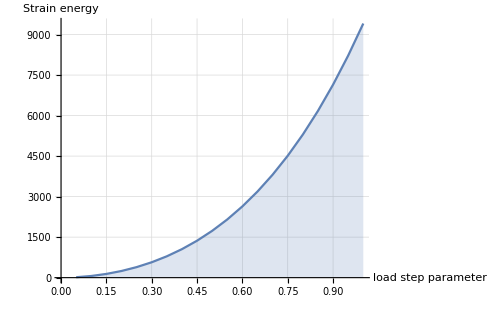
Load step param. | Strain energy
0.050 | 15.48830924419688
0.100 | 61.30405052113756
0.150 | 137.7966103225644
0.200 | 246.457019214744
0.250 | 389.5186592430581
0.300 | 569.7644572615022
0.350 | 790.4229279395326
0.400 | 1055.107816257018
0.450 | 1367.779683066066
0.500 | 1732.722722230769
0.550 | 2154.527061680917
0.600 | 2638.077810049339
0.650 | 3188.546698546632
0.700 | 3811.385967422869
0.750 | 4512.323784300536
0.800 | 5297.360918829414
0.850 | 6172.767944285168
0.900 | 7145.083202537307
0.950 | 8221.11108635943
1.000 | 9407.92067430381-Graphics-

```mathematica
LambdaList =Table[i*5/100,{i,1,20}];
SENumeric=Table[NIntegrate[SEdens/.{r->Sqrt[x^2+y^2],lambda->28.846153846153847,mu->19.230769230769230, Radius->R,d->LambdaList[[i]]},{x,y,z}∈OmegaPhys3D,AccuracyGoal->18],{i,1,Length[LambdaList]}];

tableData=Transpose[{PaddedForm[NumberForm[N[#],3],{1,3}]&/@LambdaList,NumberForm[#,18]&/@SENumeric}];
Row[{}]
```

#### 2.6.2 Relative error of the displacements in the L_2-norm

While the strain energy cannot be computed analytically for the current example, a global comparison of the analytical and numerical results is still possible, e.g., by computing the relative error of displacement in the L_2-norm via (‖u-u^h‖)_L2 / (‖u‖)_L2. Here, u^h represents the numerical solution, while u stands for the manufactured displacement field.  Due to the manufactured displacement field being a quadratic function of the radius, the symbolic integrals can be easily computed. Below, uL2NormPhys represents the symbolic expressions for (‖u(‖_L2))^2=(∫u^2dV). ⟨ Eq. (22) and Fig. 4b ⟩

```mathematica
uL2NormBox = Integrate[u[[1]]^2/.{r->Sqrt[x^2+y^2]},{x,y,z}∈OmegaBox,Assumptions->{d∈Reals,d≥0}];
uL2NormHole = Integrate[r*u[[1]]^2,{r,0,R},{phi,0,Pi/2},{z,zMin,zMax},Assumptions->{d∈Reals,d≥0}];
uL2NormPhys=(uL2NormBox-uL2NormHole)/.{Radius->R}//FullSimplify
```

-16/45 d^2 (-19408+9984 √2+3 π+5376 ArcSinh[1])